## Basic Graphics Objects

In the Wolfram Language, Circle[ ] represents a circle. To display the circle as graphics, use the function Graphics. Later, we’ll see how to specify the position and size of a circle. But for now, we’re just going to deal with a basic circle, which doesn’t need any additional input.

Make graphics of a circle:

```mathematica
Graphics[Circle[ ]]
```

-Graphics-

Disk represents a filled-in disk:

```mathematica
Graphics[Disk[ ]]
```

-Graphics-

RegularPolygon gives a regular polygon with however many sides you specify.

Here’s a pentagon (5-sided regular polygon):

```mathematica
Graphics[RegularPolygon[5]]
```

-Graphics-

Make a table of graphics of regular polygons with between 5 and 10 sides:

```mathematica
Table[Graphics[RegularPolygon[n]],{n,5,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Style works inside Graphics, so you can use it to give colors.

Here’s an orange pentagon:

```mathematica
Graphics[Style[RegularPolygon[5],Orange]]
```

-Graphics-

The Wolfram Language works in 3D as well as 2D, with constructs such as Sphere, Cylinder and Cone. When you have 3D graphics, you can rotate them around interactively to see different angles.

Display a sphere in 3D:

```mathematica
Graphics3D[Sphere[ ]]
```

-Graphics3D-

A list of a cone and a cylinder:

```mathematica
{Graphics3D[Cone[ ]],Graphics3D[Cylinder[ ]]}
```

{-Graphics3D-,-Graphics3D-}

A yellow sphere:

```mathematica
Graphics3D[Style[Sphere[ ],Yellow]]
```

-Graphics3D-

Vocabulary

Circle[ ] |   | specify a circle 
Disk[ ] |   | specify a filled-in disk 
RegularPolygon[n] |   | specify a regular polygon with n sides 
Graphics[object] |   | display an object as graphics 
Sphere[ ], Cylinder[ ], Cone[ ], ... |   | specify 3D geometric shapes 
Graphics3D[object] |   | display an object as 3D graphics

"8 Exercises Available"
"with 3 extras" | "Get Started »"

Use RegularPolygon to draw a triangle. »

| Expected output: |  
  |  |

Make graphics of a red circle. »

| Expected output: |  
  |  |

Make a red octagon. »

| Expected output: |  
  |  |

Make a list whose elements are disks with hues varying from 0 to 1 in steps of 0.1. »

| Expected output: |  
  | {,,,,,,,,,,} |

Make a column of a red and a green triangle. »

| Expected output: |  
  | 
 |

Make a list giving the regular polygons with 5 through 10 sides, with each polygon being colored pink. »

| Expected output: |  
  | {,,,,,} |

Make a graphic of a purple cylinder. »

| Expected output: |  
  | -Graphics3D- |

Make a list of polygons with 8, 7, 6, ... , 3 sides, and colored with RandomColor, then show them all overlaid with the triangle on top (hint: apply Graphics to the list). »

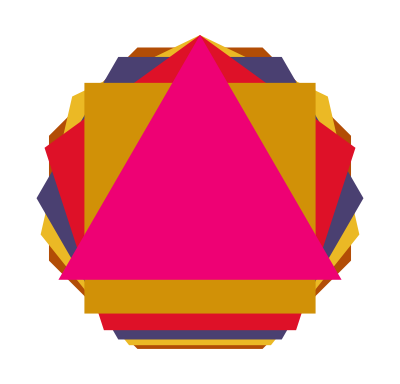
| Sample expected output: |  
  | -Graphics- |

Make a list of 10 regular pentagons with random colors.  »

| Expected output: |  
  | {,,,,,,,,,} |

Make a list of a 20-sided regular polygon and a disk. »

| Expected output: |  
  | {,} |

Make a list of polygons with 10, 9, ... , 3 sides. »

| Expected output: |  
  | {,,,,,,,} |

Q&A

How can I make graphics with several objects?

Section 14 will explain. To do so requires understanding coordinates.

Why use Circle[ ], not just Circle?

For consistency. As we’ll see in Section 14, Circle[ ] is actually short for Circle[{0,0},1], which means a circle of radius 1 and center coordinates {0,0}.

Why isn’t the yellow sphere pure yellow?

Because the Wolfram Language displays it like an actual 3D object, with lighting. If it were pure yellow, you wouldn’t see any 3D depth, and it would just look like a 2D disk.

Tech Note

Another way to specify styles for graphics is to give “directives” in a list, e.g. {Yellow,Disk[ ],Black,Circle[ ]}.

More to Explore

Guide to Graphics in the Wolfram Language »